```mathematica
AppendTo[$Path, NotebookDirectory[]];
```

```mathematica
data=Flatten[Table[{r Cos[t],r Sin[t],Sinc[r]},{r,0,10,0.5},{t,0,2Pi,0.1}],1];
```

```mathematica
speckle=Import["speckle.mat"][[1]];
```

```mathematica
eq=({{0≤y/(√3)-√(2/3) b Cos[π/6+θ]-√(2/3) a Sin[π/6+θ]≤255}, {0≤y/(√3)+√(2/3) a Cos[θ]-√(2/3) b Sin[θ]≤255}, {0≤y/(√3)+√(2/3) b Cos[π/6-θ]-√(2/3) a Sin[π/6-θ]≤255}});
InsideCubeQ[{y_,a_,b_}]:=Evaluate[Reduce[Simplify[eq/.{θ->0}],{y,a,b}]]
```

```mathematica
speckle=Select[speckle,InsideCubeQ];
```

```mathematica
Save[NotebookDirectory[]<>"speckle.nb",speckle]
```

```mathematica
speckle=speckle[[1]];
```

```mathematica
ListPointPlot3D[speckle]
```

-Graphics3D-

```mathematica
speckle[[1]]
```

```mathematica
Head[speckle]
```

List

```mathematica
speckle[[1,10]]
```

{10.,1.,1.}

```mathematica
Length[speckle]
```

3533040

```mathematica
mapYab16=Import["Transform/mapYab16.mat"][[1]];
```

```mathematica
Dimensions[mapYab16]
```

{3,16,16,16}

```mathematica
redLines=Flatten[Table[mapYab16[[All,r,g,b]],{g,1,16},{b,1,16},{r,1,16}],1];
greenLines=Flatten[Table[mapYab16[[All,r,g,b]],{r,1,16},{b,1,16},{g,1,16}],1];
blueLines=Flatten[Table[mapYab16[[All,r,g,b]],{r,1,16},{g,1,16},{b,1,16}],1];
dRanges={{Min[mapYab16[[1,All,All,All]]],Max[mapYab16[[1,All,All,All]]]},
{Min[mapYab16[[2,All,All,All]]],Max[mapYab16[[2,All,All,All]]]},
{Min[mapYab16[[3,All,All,All]]],Max[mapYab16[[3,All,All,All]]]}};
dLengths={-Min[mapYab16[[1,All,All,All]]]+Max[mapYab16[[1,All,All,All]]],
-Min[mapYab16[[2,All,All,All]]]+Max[mapYab16[[2,All,All,All]]],
-Min[mapYab16[[3,All,All,All]]]+Max[mapYab16[[3,All,All,All]]]};
ranges={{Floor[Min[mapYab16[[1,All,All,All]]]],Ceiling[Max[mapYab16[[1,All,All,All]]]]},
{Floor[Min[mapYab16[[2,All,All,All]]]],Ceiling[Max[mapYab16[[2,All,All,All]]]]},
{Floor[Min[mapYab16[[3,All,All,All]]]],Ceiling[Max[mapYab16[[3,All,All,All]]]]}};
yLine=Flatten[{Black,Table[Line[{{ranges[[1,1]],a,b},{ranges[[1,2]],a,b}}],{a,ranges[[2,1]],ranges[[2,2]]},{b,ranges[[3,1]],ranges[[3,2]]}]}];
aLine=Flatten[{Black,Table[Line[{{y,ranges[[2,1]],b},{y,ranges[[2,2]],b}}],{y,ranges[[1,1]],ranges[[1,2]]},{b,ranges[[3,1]],ranges[[3,2]]}]}];
bLine=Flatten[{Black,Table[Line[{{y,a,ranges[[3,1]]},{y,a,ranges[[3,2]]}}],{y,ranges[[1,1]],ranges[[1,2]]},{a,ranges[[2,1]],ranges[[2,2]]}]}];
```

{{0.,26.25},{0.407695,25.7202},{0.532458,22.095}}

{26.25,25.3125,21.5625}

```mathematica
ListPointPlot3D[redLines]
```

-Graphics3D-

```mathematica
redLine=Flatten[{Red,MapThread[Line[{#1,#2}]&,{redLines[[All,1,All]],redLines[[All,-1,All]]}]}];
blueLine=Flatten[{Blue,MapThread[Line[{#1,#2}]&,{blueLines[[All,1,All]],blueLines[[All,-1,All]]}]}];
greenLine=Flatten[{Green,MapThread[Line[{#1,#2}]&,{greenLines[[All,1,All]],greenLines[[All,-1,All]]}]}];
grfx={redLine,blueLine,greenLine,yLine,aLine,bLine};
Show[Graphics3D[grfx],ListPointPlot3D[redLines],ViewPoint->{0,0,Infinity},ViewVertical->{1,0,0}]
Show[Graphics3D[grfx],ListPointPlot3D[redLines],ViewPoint->{0,Infinity,0},ViewVertical->{1,0,0}]
Show[Graphics3D[grfx],ListPointPlot3D[redLines],ViewPoint->{Infinity,0,0},ViewVertical->{1,0,0}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
dRanges
```

{{0.,26.},{1.77636×10^-15,25.},{0.,22.}}

```mathematica
2^4
```

16

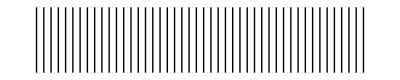

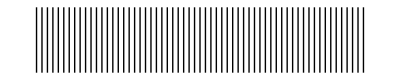

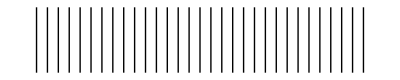

{0.577778,0.577778,0.577778,0.577778,0.577778,0.577778,0.577778}

{0.416667,0.416667,0.416667,0.416667}

{0.733333,0.733333,0.733333,0.733333}

```mathematica
yPts=Union[Flatten[mapYab16[[1,All,All,All]]]];
aPts=Union[Flatten[mapYab16[[2,All,All,All]]]];
bPts=Union[Flatten[mapYab16[[3,All,All,All]]]];
Graphics[Map[Line[{{#,0},{#,1}}]&,yPts]]
Graphics[Map[Line[{{#,0},{#,1}}]&,aPts]]
Graphics[Map[Line[{{#,0},{#,1}}]&,bPts]]
Union[Rest[yPts]-Most[yPts]]
Union[Rest[aPts]-Most[aPts]]
Union[Rest[bPts]-Most[bPts]]
```

```mathematica
Dimensions[mapYab16]
```

{3,16,16,16}

```mathematica
mapYab16[[All,10,11,12]]
```

{17.3333,13.75,10.2667}

```mathematica
Extract[mapYab16,{1;;3,1,2,3}]
```

Extract::psl1: Position specification {1 ;; 3, 1, 2, 3} in Extract[{{« 1 »}, {« 1 »}, {{{11., 11., 11., 11., 11., 11., 11., 11., 11., 11., 11., 11., 11., 11., 11., 11.}, « 14 », {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}}, « 14 », {{22., 22., 22., 22., 22., 22., 22., 22., 22., 22., 22., 22., 22., 22., 22., 22.}, « 14 », {11., 11., 11., 11., 11., 11., 11., 11., 11., 11., 11., 11., 11., 11., 11., 11.}}}}, {1 ;; 3, 1, 2, 3}] is not applicable.

Extract[1,{1;;3,1,2,3}]
 |  |  |  |

```mathematica
pos=ReleaseHold[Map[Hold[Sequence][Prepend[#,1],Prepend[#,2],Prepend[#,3]]&,Position[mapYab16[[2,All,All,All]],13.75,4]]]
Extract[mapYab16,pos]
```

{{1,1,2,3},{2,1,2,3},{3,1,2,3},{1,1,4,4},{2,1,4,4},{3,1,4,4},{1,1,6,5},{2,1,6,5},{3,1,6,5},{1,1,8,6},{2,1,8,6},{3,1,8,6},{1,1,10,7},{2,1,10,7},{3,1,10,7},{1,1,12,8},{2,1,12,8},{3,1,12,8},{1,1,14,9},{2,1,14,9},{3,1,14,9},{1,1,16,10},{2,1,16,10},{3,1,16,10},{1,2,1,3},{2,2,1,3},{3,2,1,3},{1,2,3,4},{2,2,3,4},{3,2,3,4},{1,2,5,5},{2,2,5,5},{3,2,5,5},{1,2,7,6},{2,2,7,6},{3,2,7,6},{1,2,9,7},{2,2,9,7},{3,2,9,7},{1,2,11,8},{2,2,11,8},{3,2,11,8},{1,2,13,9},{2,2,13,9},{3,2,13,9},{1,2,15,10},{2,2,15,10},{3,2,15,10},{1,3,2,4},{2,3,2,4},{3,3,2,4},{1,3,4,5},{2,3,4,5},{3,3,4,5},{1,3,6,6},{2,3,6,6},{3,3,6,6},{1,3,8,7},{2,3,8,7},{3,3,8,7},{1,3,10,8},{2,3,10,8},{3,3,10,8},{1,3,12,9},{2,3,12,9},{3,3,12,9},{1,3,14,10},{2,3,14,10},{3,3,14,10},{1,3,16,11},{2,3,16,11},{3,3,16,11},{1,4,1,4},{2,4,1,4},{3,4,1,4},{1,4,3,5},{2,4,3,5},{3,4,3,5},{1,4,5,6},{2,4,5,6},{3,4,5,6},{1,4,7,7},{2,4,7,7},{3,4,7,7},{1,4,9,8},{2,4,9,8},{3,4,9,8},{1,4,11,9},{2,4,11,9},{3,4,11,9},{1,4,13,10},{2,4,13,10},{3,4,13,10},{1,4,15,11},{2,4,15,11},{3,4,15,11},{1,5,2,5},{2,5,2,5},{3,5,2,5},{1,5,4,6},{2,5,4,6},{3,5,4,6},{1,5,6,7},{2,5,6,7},{3,5,6,7},{1,5,8,8},{2,5,8,8},{3,5,8,8},{1,5,10,9},{2,5,10,9},{3,5,10,9},{1,5,12,10},{2,5,12,10},{3,5,12,10},{1,5,14,11},{2,5,14,11},{3,5,14,11},{1,5,16,12},{2,5,16,12},{3,5,16,12},{1,6,1,5},{2,6,1,5},{3,6,1,5},{1,6,3,6},{2,6,3,6},{3,6,3,6},{1,6,5,7},{2,6,5,7},{3,6,5,7},{1,6,7,8},{2,6,7,8},{3,6,7,8},{1,6,9,9},{2,6,9,9},{3,6,9,9},{1,6,11,10},{2,6,11,10},{3,6,11,10},{1,6,13,11},{2,6,13,11},{3,6,13,11},{1,6,15,12},{2,6,15,12},{3,6,15,12},{1,7,2,6},{2,7,2,6},{3,7,2,6},{1,7,4,7},{2,7,4,7},{3,7,4,7},{1,7,6,8},{2,7,6,8},{3,7,6,8},{1,7,8,9},{2,7,8,9},{3,7,8,9},{1,7,10,10},{2,7,10,10},{3,7,10,10},{1,7,12,11},{2,7,12,11},{3,7,12,11},{1,7,14,12},{2,7,14,12},{3,7,14,12},{1,7,16,13},{2,7,16,13},{3,7,16,13},{1,8,1,6},{2,8,1,6},{3,8,1,6},{1,8,3,7},{2,8,3,7},{3,8,3,7},{1,8,5,8},{2,8,5,8},{3,8,5,8},{1,8,7,9},{2,8,7,9},{3,8,7,9},{1,8,9,10},{2,8,9,10},{3,8,9,10},{1,8,11,11},{2,8,11,11},{3,8,11,11},{1,8,13,12},{2,8,13,12},{3,8,13,12},{1,8,15,13},{2,8,15,13},{3,8,15,13},{1,9,2,7},{2,9,2,7},{3,9,2,7},{1,9,4,8},{2,9,4,8},{3,9,4,8},{1,9,6,9},{2,9,6,9},{3,9,6,9},{1,9,8,10},{2,9,8,10},{3,9,8,10},{1,9,10,11},{2,9,10,11},{3,9,10,11},{1,9,12,12},{2,9,12,12},{3,9,12,12},{1,9,14,13},{2,9,14,13},{3,9,14,13},{1,9,16,14},{2,9,16,14},{3,9,16,14},{1,10,1,7},{2,10,1,7},{3,10,1,7},{1,10,3,8},{2,10,3,8},{3,10,3,8},{1,10,5,9},{2,10,5,9},{3,10,5,9},{1,10,7,10},{2,10,7,10},{3,10,7,10},{1,10,9,11},{2,10,9,11},{3,10,9,11},{1,10,11,12},{2,10,11,12},{3,10,11,12},{1,10,13,13},{2,10,13,13},{3,10,13,13},{1,10,15,14},{2,10,15,14},{3,10,15,14},{1,11,2,8},{2,11,2,8},{3,11,2,8},{1,11,4,9},{2,11,4,9},{3,11,4,9},{1,11,6,10},{2,11,6,10},{3,11,6,10},{1,11,8,11},{2,11,8,11},{3,11,8,11},{1,11,10,12},{2,11,10,12},{3,11,10,12},{1,11,12,13},{2,11,12,13},{3,11,12,13},{1,11,14,14},{2,11,14,14},{3,11,14,14},{1,11,16,15},{2,11,16,15},{3,11,16,15},{1,12,1,8},{2,12,1,8},{3,12,1,8},{1,12,3,9},{2,12,3,9},{3,12,3,9},{1,12,5,10},{2,12,5,10},{3,12,5,10},{1,12,7,11},{2,12,7,11},{3,12,7,11},{1,12,9,12},{2,12,9,12},{3,12,9,12},{1,12,11,13},{2,12,11,13},{3,12,11,13},{1,12,13,14},{2,12,13,14},{3,12,13,14},{1,12,15,15},{2,12,15,15},{3,12,15,15},{1,13,2,9},{2,13,2,9},{3,13,2,9},{1,13,4,10},{2,13,4,10},{3,13,4,10},{1,13,6,11},{2,13,6,11},{3,13,6,11},{1,13,8,12},{2,13,8,12},{3,13,8,12},{1,13,10,13},{2,13,10,13},{3,13,10,13},{1,13,12,14},{2,13,12,14},{3,13,12,14},{1,13,14,15},{2,13,14,15},{3,13,14,15},{1,13,16,16},{2,13,16,16},{3,13,16,16},{1,14,1,9},{2,14,1,9},{3,14,1,9},{1,14,3,10},{2,14,3,10},{3,14,3,10},{1,14,5,11},{2,14,5,11},{3,14,5,11},{1,14,7,12},{2,14,7,12},{3,14,7,12},{1,14,9,13},{2,14,9,13},{3,14,9,13},{1,14,11,14},{2,14,11,14},{3,14,11,14},{1,14,13,15},{2,14,13,15},{3,14,13,15},{1,14,15,16},{2,14,15,16},{3,14,15,16},{1,15,2,10},{2,15,2,10},{3,15,2,10},{1,15,4,11},{2,15,4,11},{3,15,4,11},{1,15,6,12},{2,15,6,12},{3,15,6,12},{1,15,8,13},{2,15,8,13},{3,15,8,13},{1,15,10,14},{2,15,10,14},{3,15,10,14},{1,15,12,15},{2,15,12,15},{3,15,12,15},{1,15,14,16},{2,15,14,16},{3,15,14,16},{1,16,1,10},{2,16,1,10},{3,16,1,10},{1,16,3,11},{2,16,3,11},{3,16,3,11},{1,16,5,12},{2,16,5,12},{3,16,5,12},{1,16,7,13},{2,16,7,13},{3,16,7,13},{1,16,9,14},{2,16,9,14},{3,16,9,14},{1,16,11,15},{2,16,11,15},{3,16,11,15},{1,16,13,16},{2,16,13,16},{3,16,13,16}}

{2.,13.75,10.2667,4.,13.75,8.8,6.,13.75,7.33333,8.,13.75,5.86667,10.,13.75,4.4,12.,13.75,2.93333,14.,13.75,1.46667,16.,13.75,0.,2.,13.75,11.7333,4.,13.75,10.2667,6.,13.75,8.8,8.,13.75,7.33333,10.,13.75,5.86667,12.,13.75,4.4,14.,13.75,2.93333,16.,13.75,1.46667,4.,13.75,11.7333,6.,13.75,10.2667,8.,13.75,8.8,10.,13.75,7.33333,12.,13.75,5.86667,14.,13.75,4.4,16.,13.75,2.93333,18.,13.75,1.46667,4.,13.75,13.2,6.,13.75,11.7333,8.,13.75,10.2667,10.,13.75,8.8,12.,13.75,7.33333,14.,13.75,5.86667,16.,13.75,4.4,18.,13.75,2.93333,6.,13.75,13.2,8.,13.75,11.7333,10.,13.75,10.2667,12.,13.75,8.8,14.,13.75,7.33333,16.,13.75,5.86667,18.,13.75,4.4,20.,13.75,2.93333,6.,13.75,14.6667,8.,13.75,13.2,10.,13.75,11.7333,12.,13.75,10.2667,14.,13.75,8.8,16.,13.75,7.33333,18.,13.75,5.86667,20.,13.75,4.4,8.,13.75,14.6667,10.,13.75,13.2,12.,13.75,11.7333,14.,13.75,10.2667,16.,13.75,8.8,18.,13.75,7.33333,20.,13.75,5.86667,22.,13.75,4.4,8.,13.75,16.1333,10.,13.75,14.6667,12.,13.75,13.2,14.,13.75,11.7333,16.,13.75,10.2667,18.,13.75,8.8,20.,13.75,7.33333,22.,13.75,5.86667,10.,13.75,16.1333,12.,13.75,14.6667,14.,13.75,13.2,16.,13.75,11.7333,18.,13.75,10.2667,20.,13.75,8.8,22.,13.75,7.33333,24.,13.75,5.86667,10.,13.75,17.6,12.,13.75,16.1333,14.,13.75,14.6667,16.,13.75,13.2,18.,13.75,11.7333,20.,13.75,10.2667,22.,13.75,8.8,24.,13.75,7.33333,12.,13.75,17.6,14.,13.75,16.1333,16.,13.75,14.6667,18.,13.75,13.2,20.,13.75,11.7333,22.,13.75,10.2667,24.,13.75,8.8,26.,13.75,7.33333,12.,13.75,19.0667,14.,13.75,17.6,16.,13.75,16.1333,18.,13.75,14.6667,20.,13.75,13.2,22.,13.75,11.7333,24.,13.75,10.2667,26.,13.75,8.8,14.,13.75,19.0667,16.,13.75,17.6,18.,13.75,16.1333,20.,13.75,14.6667,22.,13.75,13.2,24.,13.75,11.7333,26.,13.75,10.2667,28.,13.75,8.8,14.,13.75,20.5333,16.,13.75,19.0667,18.,13.75,17.6,20.,13.75,16.1333,22.,13.75,14.6667,24.,13.75,13.2,26.,13.75,11.7333,28.,13.75,10.2667,16.,13.75,20.5333,18.,13.75,19.0667,20.,13.75,17.6,22.,13.75,16.1333,24.,13.75,14.6667,26.,13.75,13.2,28.,13.75,11.7333,16.,13.75,22.,18.,13.75,20.5333,20.,13.75,19.0667,22.,13.75,17.6,24.,13.75,16.1333,26.,13.75,14.6667,28.,13.75,13.2}

```mathematica
dim={Max[mapYab16[[1,All,All,All]]],Max[mapYab16[[2,All,All,All]]],Max[mapYab16[[3,All,All,All]]]}
bins=Table[0,{i,0,dim[[1]]},{j,0,dim[[2]]},{k,0,dim[[3]]}];
Dimensions[bins]
indx=Flatten[Table[Round[mapYab16[[All,r,g,b]]]+1,{r,1,n},{g,1,n},{b,1,n}],2];
{Max[indx[[All,1]]],Max[indx[[All,2]]],Max[indx[[All,3]]]}
Do[Part[bins,indx[[i,1]],indx[[i,2]],indx[[i,3]]]++,{i,1,Length[indx]}];
```

{30.,25.,22.}

{31,26,23}

{31,26,23}

```mathematica
bins
```

bins

```mathematica
{Max[indx[[All,1]]],Max[indx[[All,2]]],Max[indx[[All,3]]]}
```

{31,26,23}

```mathematica
Part[bins,indx[[2,1]],indx[[2,2]],indx[[2,3]]]++
```

4

{{1,13,12},{2,14,12},{2,15,12},{3,16,12},{4,17,12},{4,18,12},{5,19,12},{6,19,12},{6,20,12},{7,21,12},{8,22,12},{8,23,12},{9,23,12},{10,24,12},{10,25,12},{11,26,12},{2,13,11},{2,14,11},4061,{30,14,13},{21,1,12},{22,2,12},{22,3,12},{23,3,12},{24,4,12},{24,5,12},{25,6,12},{26,7,12},{26,8,12},{27,9,12},{28,9,12},{28,10,12},{29,11,12},{30,12,12},{30,13,12},{31,13,12}}
 |  |  |  |

```mathematica
n=2^4;
mapYab16=Import["Transform/mapYab16.mat"][[1]];
redLines=Flatten[Table[mapYab16[[All,r,g,b]],{g,1,n},{b,1,n},{r,1,n}],1];
greenLines=Flatten[Table[mapYab16[[All,r,g,b]],{r,1,n},{b,1,n},{g,1,n}],1];
blueLines=Flatten[Table[mapYab16[[All,r,g,b]],{r,1,n},{g,1,n},{b,1,n}],1];
dRanges={{Min[mapYab16[[1,All,All,All]]],Max[mapYab16[[1,All,All,All]]]},
{Min[mapYab16[[2,All,All,All]]],Max[mapYab16[[2,All,All,All]]]},
{Min[mapYab16[[3,All,All,All]]],Max[mapYab16[[3,All,All,All]]]}};
dLengths={-Min[mapYab16[[1,All,All,All]]]+Max[mapYab16[[1,All,All,All]]],
-Min[mapYab16[[2,All,All,All]]]+Max[mapYab16[[2,All,All,All]]],
-Min[mapYab16[[3,All,All,All]]]+Max[mapYab16[[3,All,All,All]]]};
ranges={{Floor[Min[mapYab16[[1,All,All,All]]]],Ceiling[Max[mapYab16[[1,All,All,All]]]]},
{Floor[Min[mapYab16[[2,All,All,All]]]],Ceiling[Max[mapYab16[[2,All,All,All]]]]},
{Floor[Min[mapYab16[[3,All,All,All]]]],Ceiling[Max[mapYab16[[3,All,All,All]]]]}};
yLine=Flatten[{Black,Table[Line[{{ranges[[1,1]],a,b},{ranges[[1,2]],a,b}}],{a,ranges[[2,1]],ranges[[2,2]]},{b,ranges[[3,1]],ranges[[3,2]]}]}];
aLine=Flatten[{Black,Table[Line[{{y,ranges[[2,1]],b},{y,ranges[[2,2]],b}}],{y,ranges[[1,1]],ranges[[1,2]]},{b,ranges[[3,1]],ranges[[3,2]]}]}];
bLine=Flatten[{Black,Table[Line[{{y,a,ranges[[3,1]]},{y,a,ranges[[3,2]]}}],{y,ranges[[1,1]],ranges[[1,2]]},{a,ranges[[2,1]],ranges[[2,2]]}]}];
redLine=Flatten[{Red,MapThread[Line[{#1,#2}]&,{redLines[[All,1,All]],redLines[[All,-1,All]]}]}];
blueLine=Flatten[{Blue,MapThread[Line[{#1,#2}]&,{blueLines[[All,1,All]],blueLines[[All,-1,All]]}]}];
greenLine=Flatten[{Green,MapThread[Line[{#1,#2}]&,{greenLines[[All,1,All]],greenLines[[All,-1,All]]}]}];
grfx={redLine,blueLine,greenLine,yLine,aLine,bLine};
Show[Graphics3D[grfx],ListPointPlot3D[redLines,PlotStyle->PointSize[Medium]],ViewPoint->{0,0,Infinity},ViewVertical->{1,0,0},PlotRange->{All,All,{7,8}}]
Show[Graphics3D[grfx],ListPointPlot3D[redLines,PlotStyle->PointSize[Medium]],ViewPoint->{0,Infinity,0},ViewVertical->{1,0,0},PlotRange->{All,{7,8},All}]
Show[Graphics3D[grfx],ListPointPlot3D[redLines,PlotStyle->PointSize[Medium]],ViewPoint->{Infinity,0,0},ViewVertical->{1,0,0},PlotRange->{{7,8},All,All}]
```

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification $Failed ⟦ 1 ⟧ ⟦ All, 1, 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification $Failed ⟦ 1 ⟧ ⟦ All, 2, 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification $Failed ⟦ 1 ⟧ ⟦ All, 3, 1, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification $Failed ⟦ 1 ⟧ ⟦ All, 1, 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification $Failed ⟦ 1 ⟧ ⟦ All, 1, 2, 1 ⟧ is longer than depth of object.

Part::partd: Part specification $Failed ⟦ 1 ⟧ ⟦ All, 1, 3, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification $Failed ⟦ 1 ⟧ ⟦ All, 1, 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification $Failed ⟦ 1 ⟧ ⟦ All, 1, 1, 2 ⟧ is longer than depth of object.

Part::partd: Part specification $Failed ⟦ 1 ⟧ ⟦ All, 1, 1, 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 3 of $Failed ⟦ 1 ⟧ does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 3 of $Failed ⟦ 1 ⟧ does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 3 of $Failed ⟦ 1 ⟧ does not exist.

Table::iterb: Iterator {a, Floor[Integer[]], Ceiling[Integer[]]} does not have appropriate bounds.

Table::iterb: Iterator {y, Floor[Symbol[]], Ceiling[Symbol[]]} does not have appropriate bounds.

Last::nolast: {} has a length of zero and no last element.

-Graphics3D-

Last::nolast: {} has a length of zero and no last element.

-Graphics3D-

Last::nolast: {} has a length of zero and no last element.

-Graphics3D-

```mathematica
GraphicsRow[{Show[Graphics3D[grfx],ListPointPlot3D[redLines,PlotStyle->PointSize[Medium]],ViewPoint->{0,0,Infinity},ViewVertical->{1,0,0},PlotRange->{All,All,{7,8}}],Show[Graphics3D[grfx],ListPointPlot3D[redLines,PlotStyle->PointSize[Medium]],ViewPoint->{0,Infinity,0},ViewVertical->{1,0,0},PlotRange->{All,{7,8},All}]
Show[Graphics3D[grfx],ListPointPlot3D[redLines,PlotStyle->PointSize[Medium]],ViewPoint->{Infinity,0,0},ViewVertical->{1,0,0},PlotRange->{{7,8},All,All}]}]
```

-Graphics-

```mathematica
speck16Bin=Import["Transform/speck16_Bin.mat"][[1]];
Dimensions[speck16Bin]
Max[speck16Bin]
```

{24,28,27}

5.

```mathematica
GraphicsCube[{Raster3D[speck16Bin/Max[speck16Bin],ColorFunction->"GrayLevelOpacity"]}]
```

-Graphics3D-